```mathematica
Ages2=Range[5,85,10]
```

{5,15,25,35,45,55,65,75,85}

```mathematica
mexpshort=Table[Exp[0.044Ages2[[i]]]/10,{i,Length[Ages2]}]
```

{0.124608,0.193479,0.300417,0.466459,0.724274,1.12459,1.74615,2.71126,4.2098}

```mathematica
Ems=DiagonalMatrix[mexpshort]
```

{{0.124608,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.193479,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.300417,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.466459,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.724274,0.,0.,0.,0.},{0.,0.,0.,0.,0.,1.12459,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.74615,0.,0.},{0.,0.,0.,0.,0.,0.,0.,2.71126,0.},{0.,0.,0.,0.,0.,0.,0.,0.,4.2098}}

```mathematica
FRACMreg=Drop[Import["~/Projects/MyCorona/mat_regular_10_80_V2.csv"],1,1]
```

{{4.35489,1.12877,0.691601,1.86675,1.55005,0.742783,0.33222,0.122504,0.0376935},{0.830273,11.9953,0.956307,1.08197,2.34747,0.746988,0.240643,0.229956,0.0442223},{0.332464,1.81787,4.64244,1.71435,1.81732,1.46295,0.252497,0.209775,0.152813},{1.10587,0.885478,1.90724,3.19691,2.01082,0.781121,0.894823,0.253105,0.369923},{0.652141,0.879459,1.61731,2.51354,3.61472,2.38218,0.76021,0.570157,0.0698722},{0.313956,0.413972,1.42406,1.99766,2.63286,2.57192,1.14786,0.430531,0.772306},{0.289784,0.401014,0.549972,1.27199,1.31818,0.975378,2.21875,0.580869,0.267993},{0.176859,0.179432,0.591675,1.35764,1.44575,0.990413,1.2631,1.45796,0.562091},{0.19398,0.404126,0.815436,0.829805,0.995048,1.00044,1.21956,1.30218,0.964514}}

```mathematica
FRACMLDS=Drop[Import["~/Projects/MyCorona/lockdown_SDeld20.csv"],1,1]
```

{{0.498438,0.210388,0.156954,0.417718,0.310851,0.184903,0.117344,0.0210038,0.00754654},{0.137693,1.22089,0.231941,0.215417,0.392315,0.136791,0.0654258,0.0590761,0.0114512},{0.0566076,0.522676,1.65075,0.46462,0.432301,0.284232,0.0773892,0.0849108,0.0253532},{0.273346,0.107634,0.58084,0.730349,0.499623,0.162124,0.325574,0.109569,0.0310446},{0.0818156,0.210757,0.476766,0.648246,1.01035,0.737943,0.225305,0.0800131,0.00584041},{0.124723,0.0427427,0.329765,0.421238,0.54774,0.780461,0.38986,0.100419,0.104957},{0.0884691,0.0692369,0.120624,0.326047,0.409837,0.263334,0.787624,0.129034,0.0467222},{0.0145869,0.0147278,0.0852972,0.485808,0.311168,0.203316,0.374184,0.307828,0.148389},{0.0227792,0.127426,0.179907,0.0944255,0.229148,0.17251,0.242883,0.299824,0.18637}}

```mathematica
FRACMLDnoS=Drop[Import["~/Projects/MyCorona/lockdown_noSDeld.csv"],1,1]
```

{{0.498438,0.210388,0.156954,0.417718,0.310851,0.184903,0.117344,0.0262547,0.00943318},{0.137693,1.22089,0.231941,0.215417,0.392315,0.136791,0.0654258,0.0738451,0.014314},{0.0566076,0.522676,1.65075,0.46462,0.432301,0.284232,0.0773892,0.106138,0.0316915},{0.273346,0.107634,0.58084,0.730349,0.499623,0.162124,0.325574,0.136961,0.0388057},{0.0818156,0.210757,0.476766,0.648246,1.01035,0.737943,0.225305,0.100016,0.00730051},{0.124723,0.0427427,0.329765,0.421238,0.54774,0.780461,0.38986,0.125524,0.131197},{0.0884691,0.0692369,0.120624,0.326047,0.409837,0.263334,0.787624,0.161293,0.0584027},{0.0182336,0.0184098,0.106621,0.60726,0.38896,0.254145,0.467731,0.384786,0.185486},{0.0284741,0.159282,0.224884,0.118032,0.286434,0.215637,0.303604,0.374781,0.232962}}

```mathematica
data=Drop[Import["/Users/user/Projects/MyCorona/Population/France-2019.csv"],1,1]
```

{{1875383,1793838},{2011880,1925529},{2040340,1947414},{1974988,1894312},{1867826,1830692},{1843171,1873759},{1949911,2023620},{1981008,2053344},{1969854,2020238},{2187504,2230886},{2142209,2215992},{2062831,2179885},{1891456,2060753},{1793134,2013370},{1553223,1806321},{928599,1168168},{737011,1079459},{467972,845248},{192992,462602},{50390,164018},{2811,15788}}

```mathematica
agedirFRA=Table[Sum[data[[i,k]],{i,2j-1,2j},{k,2}],{j,1,9}]
```

{7606630,7857054,7415448,8007883,8408482,8600917,7758713,5456311,3129690}

```mathematica
agedirFRA[[9]]=Sum[data[[i,k]],{i,2j-1,2j},{k,2},{j,9,10}]
```

3999692

```mathematica
data=Import["~/Projects/MyCorona/Simplified/francehosp.csv"]
```

{{reg,cl_age90,jour,hosp,rea,rad,dc},{1,0,18/03/2020,0,0,0,0},{1,9,18/03/2020,0,0,0,0},{1,19,18/03/2020,0,0,0,0},{1,29,18/03/2020,0,0,0,0},10882,{94,69,12/05/2020,11,4,30,2},{94,79,12/05/2020,18,4,35,13},{94,89,12/05/2020,12,0,32,25},{94,90,12/05/2020,8,0,13,11}}
 |  |  |  |

```mathematica
hospall=Drop[data[[All,6]],1]+Drop[data[[All,7]],1];
```

```mathematica
hosp=Table[Sum[hospall[[11 18 54+11i+j]],{i,0,17}],{j,1,11 }]
```

{74760,567,404,2091,3967,6279,10323,12851,14257,15900,7598}

```mathematica
hosppreLD=Table[Sum[hospall[[11 18 54+11i+j]],{i,0,17}],{j,1,11 }]
```

{74760,567,404,2091,3967,6279,10323,12851,14257,15900,7598}

```mathematica
hospdropfirst=Drop[hosp,1]
```

{567,404,2091,3967,6279,10323,12851,14257,15900,7598}

```mathematica
data=Drop[Import["/Users/user/Projects/MyCorona/Population/France-2019.csv"],1,1]
```

{{1875383,1793838},{2011880,1925529},{2040340,1947414},{1974988,1894312},{1867826,1830692},{1843171,1873759},{1949911,2023620},{1981008,2053344},{1969854,2020238},{2187504,2230886},{2142209,2215992},{2062831,2179885},{1891456,2060753},{1793134,2013370},{1553223,1806321},{928599,1168168},{737011,1079459},{467972,845248},{192992,462602},{50390,164018},{2811,15788}}

```mathematica
Dimensions[data]
```

{21,2}

```mathematica
Pop=Flatten[{Table[Sum[data[[i,k]],{i,2j-1,2j},{k,2}],{j,1,10}]}]
```

{7606630,7857054,7415448,8007883,8408482,8600917,7758713,5456311,3129690,870002}

```mathematica
Pop[[10]]=Sum[data[[i,k]],{i,2 10-1,Length[data]},{k,2}]
```

888601

```mathematica
hospFRA=Transpose[{Range[5,95,10],100000hospdropfirst/Pop}]
```

{{5,5670000/760663},{15,20200000/3928527},{25,8712500/308977},{35,396700000/8007883},{45,313950000/4204241},{55,1032300000/8600917},{65,1285100000/7758713},{75,1425700000/5456311},{85,53000000/104323},{95,759800000/888601}}

```mathematica
normFRA=hospFRA[[6,2]]/Exp[0.044  55]

CMnormFRA=hospFRA[[4,2]]/( Ems.Chop[Eigenvectors[Ems.(FRACMreg+Transpose[FRACMreg])]][[1]]/agedirFRA)[[5]]
```

10.6726

-3.04051×10^9

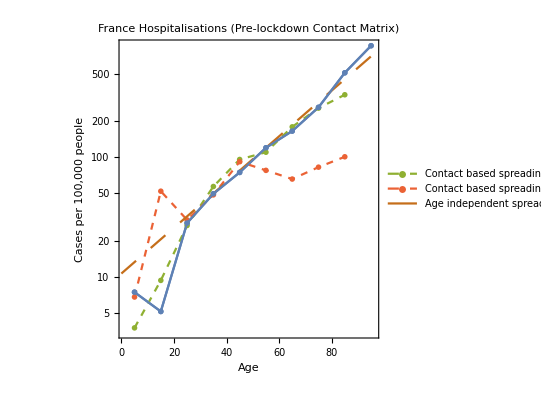

```mathematica
Show[ListLogPlot[{hospFRA},Joined->True,PlotMarkers->"OpenMarkers",PlotLabel->"France Hospitalisations (Pre-lockdown Contact Matrix)",PlotRange->{{1,96},All},Frame->{{True,False},{True,False}},FrameLabel->{{"Cases per 100,000 people",None},{"Age",None}},AspectRatio->1],ListLogPlot[{Transpose[{Ages2,0 CMnormFRA Chop[Eigenvectors[Ems.(0FRACMreg+Transpose[FRACMreg])]][[1]]/agedirFRA}],Transpose[{Ages2,0 CMnormFRA Chop[Eigenvectors[Ems.(0FRACMreg+Transpose[FRACMreg])]][[1]]/agedirFRA}],Transpose[{Ages2,-0.9 CMnormFRA Chop[Eigenvectors[Ems.(0FRACMreg+Transpose[FRACMreg])]][[1]]/agedirFRA}],Transpose[{Ages2,-0.9 CMnormFRA Ems.Chop[Eigenvectors[(0FRACMreg+Transpose[FRACMreg])]][[1]]/agedirFRA}]},PlotMarkers->"OpenMarkers",Joined->True,PlotStyle->Dashed,PlotLegends->{None,None,"Contact based spreading (no mild transmission)","Contact based spreading (full mild transmission)"}],LogPlot[{None,None,None,None,None,normFRA Exp[0.044 t]},{t,0,100}, 
 PlotStyle -> { Dashing[Large]},PlotLegends->{None,None,None,None,None,"Age independent spreading "}],ListLogPlot[{hospFRA},Joined->True,PlotMarkers->"OpenMarkers"]]
```

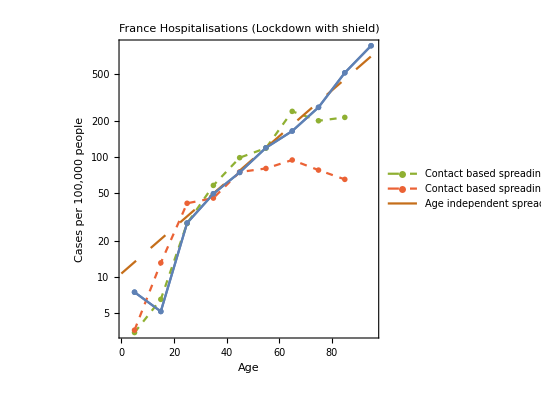

```mathematica
Show[ListLogPlot[{hospFRA},Joined->True,PlotMarkers->"OpenMarkers",PlotLabel->"France Hospitalisations (Lockdown with shield)",PlotRange->{{1,96},All},Frame->{{True,False},{True,False}},FrameLabel->{{"Cases per 100,000 people",None},{"Age",None}},AspectRatio->1],ListLogPlot[{ Transpose[{Ages2,0 CMnormFRA Chop[Eigenvectors[Ems.(0FRACMLDS+Transpose[FRACMLDS])]][[1]]/agedirFRA}],Transpose[{Ages2,0CMnormFRA Chop[Eigenvectors[Ems.(0FRACMLDS+Transpose[FRACMLDS])]][[1]]/agedirFRA}],Transpose[{Ages2,-0.9 CMnormFRA Chop[Eigenvectors[Ems.(0FRACMLDS+Transpose[FRACMLDS])]][[1]]/agedirFRA}],Transpose[{Ages2,0.6 CMnormFRA Ems.Chop[Eigenvectors[(0FRACMLDS+Transpose[FRACMLDS])]][[1]]/agedirFRA}]},PlotMarkers->"OpenMarkers",Joined->True,PlotStyle->Dashed,PlotLegends->{ None,None,"Contact based spreading (no mild transmission)","Contact based spreading (full mild transmission)"}],LogPlot[{None,None,None,None,None,normFRA Exp[0.044 t]},{t,0,100}, 
 PlotStyle -> { Dashing[Large]},PlotLegends->{None,None,None,None,None,"Age independent spreading "}],ListLogPlot[{hospFRA},Joined->True,PlotMarkers->"OpenMarkers"]]
```

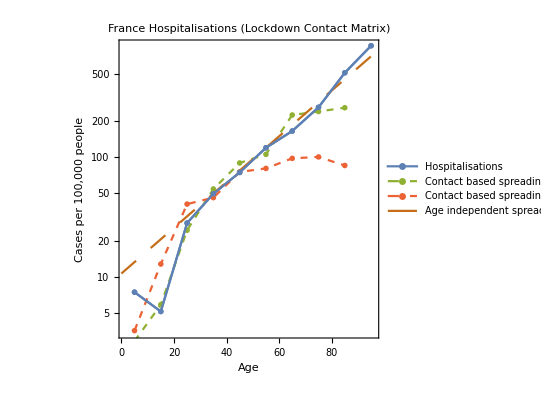

```mathematica
Show[ListLogPlot[{hospFRA},Joined->True,PlotMarkers->"OpenMarkers",PlotLabel->"France Hospitalisations (Lockdown Contact Matrix)",PlotRange->{{1,96},All},Frame->{{True,False},{True,False}},FrameLabel->{{"Cases per 100,000 people",None},{"Age",None}},AspectRatio->1,PlotLegends->{"Hospitalisations"}],ListLogPlot[{Transpose[{Ages2,0CMnormFRA Chop[Eigenvectors[Ems.(0FRACMLDnoS+Transpose[FRACMLDnoS])]][[1]]/agedirFRA}],Transpose[{Ages2,0CMnormFRA Chop[Eigenvectors[Ems.(0FRACMLDnoS+Transpose[FRACMLDnoS])]][[1]]/agedirFRA}],Transpose[{Ages2,-0.9CMnormFRA Chop[Eigenvectors[Ems.(0FRACMLDnoS+Transpose[FRACMLDnoS])]][[1]]/agedirFRA}],Transpose[{Ages2,0.6CMnormFRA Ems.Chop[Eigenvectors[(0FRACMLDnoS+Transpose[FRACMLDnoS])]][[1]]/agedirFRA}]},PlotMarkers->"OpenMarkers",Joined->True,PlotStyle->Dashed,PlotLegends->{None,None,"Contact based spreading (no mild transmission)","Contact based spreading (full mild transmission)"}],LogPlot[{None,None,None,None,None,normFRA Exp[0.044 t]},{t,0,100}, 
 PlotStyle -> { Dashing[Large]},PlotLegends->{None,None,None,None,None,"Age independent spreading "}],ListLogPlot[{hospFRA},Joined->True,PlotMarkers->"OpenMarkers"]]
```